```mathematica
SetDirectory["C:\\Users\\pglpm\\repositories\\genobayes\\scripts"]
```

C:\Users\pglpm\repositories\genobayes\scripts

```mathematica
np[i_]=(95-i)*Min[2^i,6029]
```

(95-i) Min[6029,2^i]

```mathematica
proc[i_,t_]=If[i<t,Ceiling[(95-i)/30]*Min[2^i,6029],(95-i)*Ceiling[Min[2^i,6029]/30]]
```

If[i<t,Ceiling[(95-i)/30] Min[2^i,6029],(95-i) Ceiling[1/30 Min[2^i,6029]]]

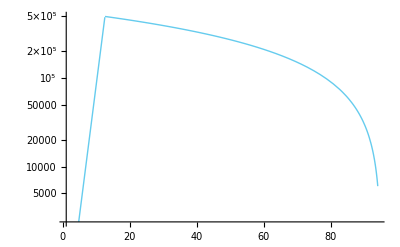

```mathematica
LogPlot[np[i],{i,1,94}]
```

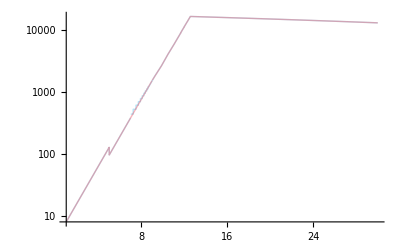

```mathematica
LogPlot[Evaluate@Table[proc[i,j],{j,{7,9}}],{i,1,30},PlotStyle->Opacity[0.5]]
```

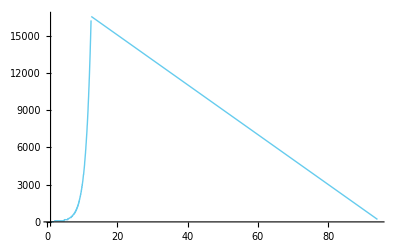

```mathematica
Plot[proc[i,2],{i,1,94}]
```

```mathematica
Log[2,60]//N
```

5.90689

```mathematica
dat={{9,0.00714046542517943},
{67,0.0127163891128827},
{13,0.0179126859494412},
{16,0.0227845604840928},
{17,0.0294803261346076},
{59,0.0361630556097422},
{70,0.0497722057835426},
{39,0.075958527360365},
{43,0.120455929312026}};
```

```mathematica
T[{Range[1,9],ToString/@dat[[;;,1]]}]
```

{{1,9},{2,67},{3,13},{4,16},{5,17},{6,59},{7,70},{8,39},{9,43}}

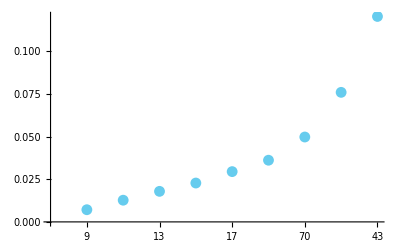

```mathematica
ListPlot[dat[[;;,2]],Ticks->{T[{Range[1,9],ToString/@dat[[;;,1]]}],Auto}]
```

```mathematica
NS["study_pairgenes"]
```

```mathematica
res=Import["results_pairs2.csv"];resh=T@Import["results_pairs_d.csv"];
```

```mathematica
Dimensions[res]
```

{4371,3}

```mathematica
Dimensions[resh]
```

{4371,3}

```mathematica
{Min@res[[;;,3]],Max@res[[;;,3]]}
```

{0.00009995,0.00428197}

```mathematica
{Min@resh[[;;,3]],Max@resh[[;;,3]]}
```

{0.000274451,0.00381057}

```mathematica
Log[10,%]
```

{-4.00022,-2.36836}

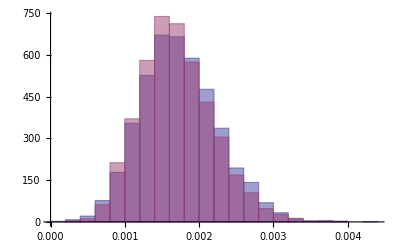

```mathematica
Histogram[{res[[;;,3]],resh[[;;,3]]},"Knuth",PlotRange->All]
```

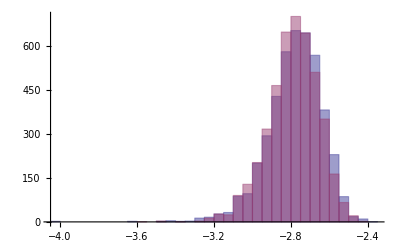

```mathematica
Histogram[{Log[10,res[[;;,3]]],Log[10,resh[[;;,3]]]},"Knuth",PlotRange->All]
```

```mathematica
sortres=Sort[res,#1[[3]]>#2[[3]]&];sortresh=Sort[resh,#1[[3]]>#2[[3]]&];
```

```mathematica
sortres[[1;;20,;;]]//MF
```

(68 | 89 | 0.00428197
88 | 89 | 0.00392101
59 | 90 | 0.00391304
32 | 89 | 0.00383417
59 | 89 | 0.00378546
89 | 90 | 0.00376354
64 | 89 | 0.0037567
72 | 89 | 0.00361801
6 | 57 | 0.00361688
61 | 88 | 0.00359064
69 | 89 | 0.00356539
9 | 58 | 0.00352329
32 | 66 | 0.00349298
34 | 89 | 0.00337852
46 | 90 | 0.00337457
31 | 66 | 0.00331328
6 | 53 | 0.0033014
6 | 21 | 0.00327939
42 | 68 | 0.00327784
9 | 38 | 0.00327634)

```mathematica
sortresh[[1;;20,;;]]//MF
```

(32 | 66 | 0.00381057
6 | 57 | 0.00370412
6 | 75 | 0.0034386
9 | 58 | 0.0034035
32 | 89 | 0.00337533
6 | 53 | 0.00337451
6 | 21 | 0.00334941
56 | 75 | 0.00331217
42 | 68 | 0.00330793
66 | 75 | 0.00329967
42 | 70 | 0.00327122
32 | 79 | 0.00326723
31 | 66 | 0.00326035
32 | 46 | 0.00325737
9 | 38 | 0.00325246
6 | 66 | 0.00323323
53 | 68 | 0.0032051
6 | 55 | 0.00319876
32 | 57 | 0.00319819
6 | 79 | 0.00319812)

```mathematica
94*93/2
```

4371

```mathematica
tab=Table[Tally[Flatten@sortres[[1;;i,1;;2]]],{i,12}];
```

```mathematica
tab[[10]]
```

{{68,1},{89,7},{88,2},{59,2},{90,2},{32,1},{64,1},{72,1},{6,1},{57,1},{61,1}}

```mathematica
tabh=Table[Tally[Flatten@sortresh[[1;;i,1;;2]]],{i,60}];
```

```mathematica
tabh[[10]]
```

{{32,2},{66,2},{6,4},{57,1},{75,3},{9,1},{58,1},{89,1},{53,1},{21,1},{56,1},{42,1},{68,1}}

```mathematica
tab2=Table[Union[Flatten@sortres[[1;;i,1;;2]]],{i,60}];
```

```mathematica
best={};i=1;While[Length@best<10,best=Union[Flatten@sortres[[1;;i,1;;2]]];i=i+1];best
```

{6,32,57,59,64,68,72,88,89,90}

```mathematica
besth={};i=1;While[Length@besth<10,besth=Union[Flatten@sortresh[[1;;i,1;;2]]];i=i+1];besth
```

{6,9,21,32,53,57,58,66,75,89}

```mathematica
best2={};i=1;While[sortres[[i,3]]>0.003,best2=Union[Flatten@sortres[[1;;i,1;;2]]];i=i+1];Length@best2
```

45

```mathematica
best2
```

{3,6,9,16,17,20,21,26,30,31,32,33,34,35,38,42,46,51,52,53,55,57,58,59,61,64,66,67,68,69,70,72,75,77,78,79,82,83,85,88,89,90,91,92,93}

```mathematica
sin=Flatten@Import["results_single_d.csv"];sinh=Flatten@Import["results_single.csv"];
max=1.73891986550377;
```

```mathematica
Dimensions[sin]
```

{94}

```mathematica
BarChart
```

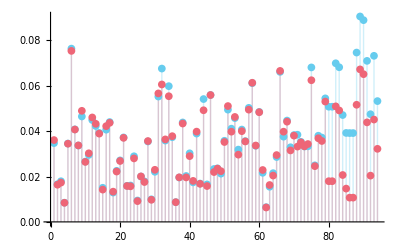

```mathematica
ListPlot[{sin,sinh}/max*100,PlotRange->All,Filling->Axis]
```

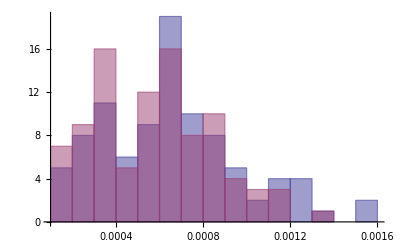

```mathematica
Histogram[{sin,sinh},"Knuth",PlotRange->All]
```

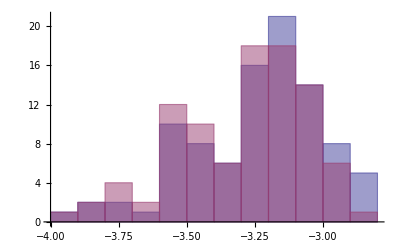

```mathematica
Histogram[{Log[10,sin],Log[10,sinh]},"Knuth",PlotRange->All]
```

```mathematica
(sortsin={Ordering[sin,Length[sin],Greater],Sort[sin,Greater]/max*100})//T//MF
```

(89 | 0.0905244
90 | 0.0888964
6 | 0.076354
88 | 0.0746155
93 | 0.0731819
91 | 0.0709536
82 | 0.0698998
83 | 0.0681401
75 | 0.0680659
32 | 0.0675649
66 | 0.0660969
58 | 0.0611441
34 | 0.0598077
46 | 0.0559065
31 | 0.0552307
79 | 0.0544321
44 | 0.0541312
94 | 0.0532323
81 | 0.0507453
80 | 0.0507453
57 | 0.0502537
51 | 0.0494584
60 | 0.0484634
92 | 0.0474514
84 | 0.0470852
9 | 0.0464522
53 | 0.0457291
12 | 0.044894
68 | 0.0446484
17 | 0.0439998
38 | 0.0438156
13 | 0.0422531
52 | 0.0410786
7 | 0.0407697
55 | 0.0406823
16 | 0.0406269
85 | 0.0391991
14 | 0.0391955
87 | 0.0391385
86 | 0.0391385
42 | 0.0389194
71 | 0.0384131
70 | 0.038257
77 | 0.0379722
67 | 0.0375427
35 | 0.0373147
21 | 0.0372193
78 | 0.0371599
33 | 0.0358261
50 | 0.0357378
56 | 0.0355888
28 | 0.035431
72 | 0.0352777
1 | 0.0347141
5 | 0.0345186
8 | 0.033662
59 | 0.0335307
74 | 0.033315
73 | 0.0332384
69 | 0.032886
54 | 0.0318592
40 | 0.0302158
11 | 0.0295236
24 | 0.0289173
65 | 0.0285811
20 | 0.0271048
10 | 0.0265704
76 | 0.024925
48 | 0.0235733
47 | 0.023315
19 | 0.0225003
30 | 0.0220714
61 | 0.0216346
64 | 0.0214696
49 | 0.021257
39 | 0.020236
26 | 0.0199926
37 | 0.0195711
3 | 0.017909
27 | 0.0178447
41 | 0.0174196
43 | 0.0168969
2 | 0.0166193
45 | 0.0165179
23 | 0.0160339
22 | 0.0158946
63 | 0.0154902
15 | 0.0150352
18 | 0.0129131
29 | 0.00993827
25 | 0.00943111
36 | 0.00870157
4 | 0.00845655
62 | 0.00649434)